```mathematica
Print["H(x,t)"];


file="/Users/vpk/Google\ Drive/Jlab/Projects/Mathematica/densities.txt";
Hdata=ReadList[file,{Number,Number,Number,Number,Number}];
x=Hdata[[All,1]];
HProfileu=Hdata[[All,2]];
HForwardu=Hdata[[All,2]];
HProfiled=Hdata[[All,3]];
HForwardd=Hdata[[All,4]];
xmin=1.9924×10^-5;
xmax=0.5;
ymin=0;
ymax=15;
HFu=Interpolation[Thread[{x,HForwardu}],InterpolationOrder->1];
HFd=Interpolation[Thread[{x,HForwardd}],InterpolationOrder->1];
HPu=Interpolation[Thread[{x,HProfileu}],InterpolationOrder->1];
HPd=Interpolation[Thread[{x,HProfiled}],InterpolationOrder->1];
Hu[x_,t_]:=HFu[x]*Exp[HPu[x]*t];
Hd[x_,t_]:=HFd[x]*Exp[HPd[x]*t];

PlotFL=Plot[{HFu[x],HFd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Forward Limit"},PlotLegends->Placed[{"u quark","d quark"},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Forward Limit"];
PlotPF=Plot[{HPu[x],HPd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Profile FUnction"},PlotLegends->Placed[{"u quark","d quark"},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Profile Function"];
xx=0.1;
 PlotH=Plot[{Hu[xx,-t],Hd[xx,-t]},{t,0,1},FrameLabel->{"-t","H(x=0.1,-t"},PlotLegends->Placed[{"u quark","d quark"},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel-> "H(x=0.1,-t)"];
(*GraphicsRow[{PlotFL,PlotPF, PlotH},ImageSize->Large]*)

(*PlotFL        PlotPF 
 PlotH *)
```

H(x,t)

"

H(x,t)

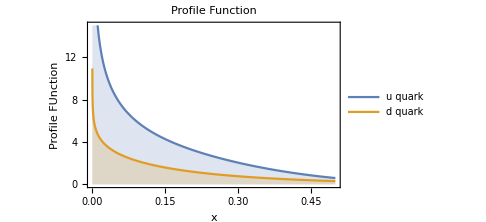
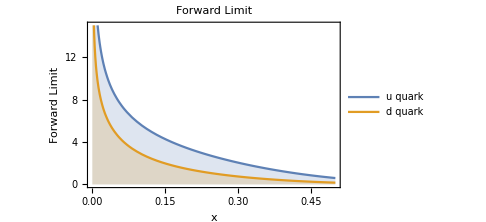

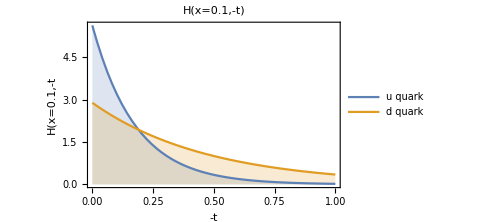

```mathematica
Print["H(x,t)"];
PlotFL        PlotPF 
 PlotH
```